

```mathematica
Plot[Sin[t],{t,0,2 Pi}]
```

```mathematica
tunnelwidth = 0.2;
d = 7;
z[d_]:=Sqrt[10^2 -d^2]; 
Manipulate[Graphics[{Point[{0,10Cos[t]}],Point[{d,z[d]Cos[t]}],Circle[{0,0},10],Line[{{tunnelwidth,-10},{tunnelwidth,10}}],Line[{{-tunnelwidth,-10},{-tunnelwidth,10}}], Line[{{d+tunnelwidth,-z[d+tunnelwidth]},{d+tunnelwidth,z[d+tunnelwidth]}}],Line[{{d-tunnelwidth,-z[d-tunnelwidth]},{d-tunnelwidth,z[d-tunnelwidth]}}]}],{t,0,2 Pi}]
```

```mathematica
Eff =Import["/home/nicolas/Documents/Physics/Bachelors-Dissertation/Trajectories/data.csv", "Table"];
EffectiveTrajectory = Interpolation[Eff,InterpolationOrder->5]
```

InterpolatingFunction[…]

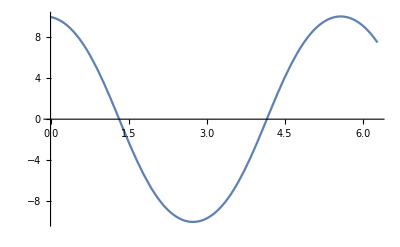

```mathematica
Plot[EffectiveTrajectory[t],{t,0,2 Pi}]
```

```mathematica
+
```